# Unit 5 - The Derivative and Tangent Lines

Topics covered in this unit are listed below.

Review

Finding equations of secant and tangent lines

Finding the derivative by Mathematica commands

Finding higher-order derivatives

Finding inflection points

Finding equations of tangent lines using derivative

Three difference quotients

## Review

By definition, if the limit lim_(h→0) (f(a+h)-f(a))/hexists, f(x) is said to be differentiable at x=a, and the limit is called the derivative of f(x) at x=a, denoted by f'(a).

Depending on the context, f'(a) indicates typically the slope of the tangent line to the curve of f(x), the speed of a moving particle of which the position function is governed by f(x), or the rate of change of y with respect to x, at x=a.

A typical application in calculus is to find the equation of the tangent line to the curve of a function at a point. A straight line could usually be described by y=m x+b or y-y_0=m (x-x_0), i.e, y=y_0+m (x-x_0), where m is its slope, b is its y-intercept, and (x_0,y_0) is a given point on the line. In our case here, the equation of the tangent line to the curve of f(x) at x_0 is

y=f(x_0)+f'(x_0)(x-x_0) ⋯⋯⋯⋯⋯⋯⋯⋯⋯⋯ (1)

The slope of the straight line passing through two points (x_1,y_1) and (x_2,y_2) is given by

m=(y_2-y_1)/(x_2-x_1).

The secant line of the curve y=f(x) connecting (x_1,f(x_1))  and (x_2,f(x_2)) is

y=f(x_1)+(f(x_2)-f(x_1))/(x_2-x_1)(x-x_1) or y=f(x_2)+(f(x_2)-f(x_1))/(x_2-x_1)(x-x_2).

If x_2 is close to x_1, we may use the secant line passing through (x_1,f(x_1))  and (x_2,f(x_2)) to approximate the tangent line to f(x) at x=x_1. Let h=x_2-x_1. The tangent line is approximated by the secant line

y=f(x_1)+(f(x_1+h)-f(x_1))/h(x-x_1) ⋯⋯⋯⋯⋯⋯⋯⋯ (2)

## Finding equations of secant and tangent lines

Example 1
For f(x)=x^2, find the equation of the secant line through (-1,f(-1)) and (2,f(2)).

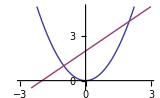

The secant line is y = x+2

```mathematica
f[x_]:=x^2
g[x_]:=Module[{x1=-1,x2=2},f[x1]+(f[x2]-f[x1])/(x2-x1)(x-x1)] (* secant line*)
Plot[{f[x],g[x]},{x,-3,3},PlotRange->{-0.5,5},ImageSize->160]
Print["The secant line is y = ", TraditionalForm[g[x]]]
```

Example 2
For f(x)=x^2, find the equation of the secant line through (-1,f(-1)) and (-1+h,f(-1+h)).

```mathematica
f[x_]:=x^2
g[x_]:=Module[{x1=-1},f[x1]+(f[x1+h]-f[x1])/h(x-x1)] (* secant line*)
Print["The secant line is y = ", TraditionalForm[g[x]]]
```

The secant line is y = (((h-1)^2-1) (x+1))/h+1

Example 3
Use animation to explore the secant lines of f(x)=x^2 near x=-1.

From Example 2, we make animation using various values of h.

```mathematica
Manipulate[
Module[{f,g,k,x0=-1,xmin=-3,xmax=3,ymin=-2.5,ymax=5},
f[x_]:=x^2;

x0=-1; (* explore the tangent line approximation at (Subscript[x, 0],f(Subscript[x, o])) *)
xmin=-3;xmax=3; (* plot for xmin≤ x ≤ xmax *)
ymin=-2.5;ymax=5; (* PlotRange->{ymin, ymax} *)

g[x_,h_]:=f[x0]+(f[x0+h]-f[x0])/h(x-x0) ; (* equation of secant line *)
k[x_]:=Module[{h},Limit[g[x,h],h->0]];

Show[
Plot[{f[x],g[x,h],k[x]},{x,xmin,xmax},PlotRange->{ymin,ymax},PlotStyle->{{Blue},{Red},{Blue,Dashed,Thick}},ImageSize->300],
Graphics[Text[StringJoin["h = ",ToString[h]],{-1,4}]],
Graphics[{Black, Arrow[{{xmin,0},{xmax,0}}]}],
Graphics[{Black, Arrow[{{0,ymin},{0,ymax}}]}],
Graphics[{Blue,PointSize[Large],Point[{x0,0}]}],
Graphics[{Blue,PointSize[Large],Point[{x0,f[x0]}]}],
Graphics[{Red,PointSize[Large],Point[{x0+h,f[x0+h]}]}],
Graphics[{Red,PointSize[Large],Point[{x0+h,0}]}],
Graphics[{Blue,Dashed, Line[{{x0,0},{x0,f[x0]}}]}],
Graphics[{Red,Dashed, Line[{{x0+h,0},{x0+h,f[x0+h]}}]}]
]],
{{h,0.999},-1.201,3.2,0.002}] (* make sure that h will not become zero *)
```

Example 4
For f(x)=x^2, find the equation of the tangent line at x=-1.

From Example 2, the tangent line is the limiting case of the secant line as h→0. Thus,

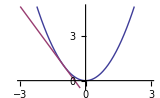

The secant line is y = -2 x-1

```mathematica
Clear[x,y,h]
f[x_]:=x^2
g[x_]:=Limit[Module[{x1=-1},f[x1]+(f[x1+h]-f[x1])/h(x-x1)] ,h->0]
Plot[{f[x],g[x]},{x,-3,3},PlotRange->{-0.5,5},ImageSize->160]
Print["The secant line is y = ", TraditionalForm[g[x]]]
```

## Finding the derivative by Mathematica commands

We don’t have to follow the definition of the derivative and evaluate the limiting value of the difference quotient at h→0 each time. Mathematica provides commands to facilitate the computation.

Given that f(x) is differentiable at x, corresponding to different notations of the derivative, f'(x) can be obtained by one of the following commands:

f'[x]
D[f[x],x]
∂_x f[x]

For example,

```mathematica
f[x_]:=x^2 ⅇ^x
f'[x]
```

2 ⅇ^x x+ⅇ^x x^2

```mathematica
D[f[x],x]
```

2 ⅇ^x x+ⅇ^x x^2

```mathematica
D[f[x], x]
```

2 ⅇ^x x+ⅇ^x x^2

```mathematica
D[{Sin[2x],ⅇ^x Cos[3x],Sqrt[1-x^2]},x]
```

{2 Cos[2 x],ⅇ^x Cos[3 x]-3 ⅇ^x Sin[3 x],-x/(√(1-x^2))}

Example 4
Use Mathematica command to find f'(π/2) for f(x)=x^2 sin x.

```mathematica
f[x_]:=x^2 Sin[x]
D[f[x],x]
```

x^2 Cos[x]+2 x Sin[x]

```mathematica
%/.x->π/2
```

π

Remember that Mathematica does not simplify symbolic result automatically. So, when we do symbolic computing, we have to apply Simply often.

Example 5

```mathematica
f[x_]:=x Sin[2x]^2+x Cos[2x]^2
D[f[x],x]
```

Cos[2 x]^2+Sin[2 x]^2

```mathematica
%//Simplify
```

1

Mathematica is such a powerful computer algebra system that it is able to compute symbolically the derivative of very complicated functions.

Example 6

```mathematica
D[(Sec[x]Tan[x])/(x+√(1-x^2)),x]//Simplify
```

(Sec[x] ((x+√(1-x^2)) Sec[x]^2+Tan[x] (-1+x/(√(1-x^2))+(x+√(1-x^2)) Tan[x])))/((x+√(1-x^2))^2)

## Finding higher-order derivatives

The following Mathematica commands will be used,

f''[x], f'''[x],⋯
D[f[x],{x,n}](* the nth order derivative of f(x) *)
∂_(x,x),∂_(x,x,x),⋯

Example 7
Find f''(π/2) for f(x)=x^2 sin x.

```mathematica
f[x_]:=x^2 Sin[x]
f''[x]
```

4 x Cos[x]+2 Sin[x]-x^2 Sin[x]

```mathematica
%/.x->π/2
```

2-π^2/4

```mathematica
D[f[x],{x,2}]/.x->π/2
```

2-π^2/4

```mathematica
D[f[x], x,x]/.x->π/2
```

2-π^2/4

Similarly, we can find the third or even higher order derivatives.

Example 8

```mathematica
f[x_]:=ⅇ^(2x)
Table[D[f[x],{x,n}],{n,1,20}]
```

{2 ⅇ^(2 x),4 ⅇ^(2 x),8 ⅇ^(2 x),16 ⅇ^(2 x),32 ⅇ^(2 x),64 ⅇ^(2 x),128 ⅇ^(2 x),256 ⅇ^(2 x),512 ⅇ^(2 x),1024 ⅇ^(2 x),2048 ⅇ^(2 x),4096 ⅇ^(2 x),8192 ⅇ^(2 x),16384 ⅇ^(2 x),32768 ⅇ^(2 x),65536 ⅇ^(2 x),131072 ⅇ^(2 x),262144 ⅇ^(2 x),524288 ⅇ^(2 x),1048576 ⅇ^(2 x)}

```mathematica
%/.x->0 (* evaluating f'(0),f''(0),... *)
```

{2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384,32768,65536,131072,262144,524288,1048576}

Can we find a general formula for f^(n)(0)? It seems to be f^(n)(0)=2^n,n=1,2,3,⋯. Using this formula, we can use Table to create a list to verity if it is correct or not.

```mathematica
Table[2^n,{n,1,20}]
```

{2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384,32768,65536,131072,262144,524288,1048576}

Well done!

Example 9
Given that f(x)=ⅇ^x sin x, find f'(x), f''(x),f'''(x),⋯ at x=0.

```mathematica
f[x_]:=ⅇ^x Sin[x]
Table[D[f[x],{x,n}],{n,1,20}]//Simplify
```

{ⅇ^x (Cos[x]+Sin[x]),2 ⅇ^x Cos[x],2 ⅇ^x (Cos[x]-Sin[x]),-4 ⅇ^x Sin[x],-4 ⅇ^x (Cos[x]+Sin[x]),-8 ⅇ^x Cos[x],-8 ⅇ^x (Cos[x]-Sin[x]),16 ⅇ^x Sin[x],16 ⅇ^x (Cos[x]+Sin[x]),32 ⅇ^x Cos[x],32 ⅇ^x (Cos[x]-Sin[x]),-64 ⅇ^x Sin[x],-64 ⅇ^x (Cos[x]+Sin[x]),-128 ⅇ^x Cos[x],-128 ⅇ^x (Cos[x]-Sin[x]),256 ⅇ^x Sin[x],256 ⅇ^x (Cos[x]+Sin[x]),512 ⅇ^x Cos[x],512 ⅇ^x (Cos[x]-Sin[x]),-1024 ⅇ^x Sin[x]}

```mathematica
%/.x->0
```

{1,2,2,0,-4,-8,-8,0,16,32,32,0,-64,-128,-128,0,256,512,512,0}

Can you figure out the pattern in these values? What will be f^(21)(0), f^(22)(0), f^(23)(0), f^(24)(0)? 

The list shows obviously that the pattern is based on a group of four elements. Therefore, the pattern can be expressed by f^(4n+1) , f^(4n+2),f^(4n+3),f^(4n+4),n=0,1,2,⋯

Answer: f^(4n+1)(0) = (-1)^n 4^n, f^(4n+2)(0) =2 (-1)^n 4^n,f^(4n+3)(0) =2 (-1)^n 4^n,f^(4n+4)(0) =0,n=0,1,2,⋯ ;
              -1024, -2048, -2048, 0.

We can verify if the pattern is correct by using Table to generate a partial list and comparing the two lists.

```mathematica
Table[{(-1)^n 4^n,2(-1)^n 4^n,2(-1)^n 4^n,0},{n,0,5}]
```

{{1,2,2,0},{-4,-8,-8,0},{16,32,32,0},{-64,-128,-128,0},{256,512,512,0},{-1024,-2048,-2048,0}}

```mathematica
%//Flatten
```

{1,2,2,0,-4,-8,-8,0,16,32,32,0,-64,-128,-128,0,256,512,512,0,-1024,-2048,-2048,0}

Example 10
Explore visually the relation between f(x) and f'(x) and the relation between f(x) and f''(x). Take f(x)=sin x over [-π,π] as the example,

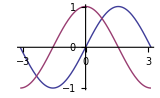

```mathematica
f[x_]:=Sin[x]
Plot[{f[x],f'[x]},{x,-Pi,Pi},ImageSize->160]
```

A basic phenomenon is that, if f(x) is increasing, f'(x) is positive and its curve is above the x-axis; if f(x) is decreasing, f'(x) is negative and its curve is below the x-axis.

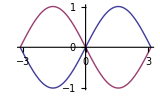

```mathematica
Plot[{f[x],f''[x]},{x,-Pi,Pi},ImageSize->160]
```

Now, when f(x) is concave upward, f''(x) is positive and its curve is above the x-axis; when f(x) is concave downward, f''(x) is negative and its curve is below the x-axis.

## Finding inflection points

What is an inflection point of f(x)? It is the point on the curve of f(x) at which the concavity changes from being concave upward to downward, or vice versa. The procedure of finding inflection points as follows.

Find f''(x).

Find all possible inflection points by solving f''(x)=0 for x=x_1,x_2,⋯,x_n. (Imagine that there are two more points in the sequence, i.e., x_0=-∞ and x_(n+1)=∞.)

Investigate each x_i,i=1,2,⋯,n

Choose any point a∈(x_(i-1),x_i) and any point b∈(x_i,x_(i+1)) , and evaluate f''(a) and f''(b).

If f''(a)×f''(b)>0, the two second-order derivatives have the same sign, i.e., no concavity changes, then x_i is not an inflection point; otherwise, it is an inflection point.

Example 11
Find the inflection points of f(x)=x+cos x on the interval [0,2π].

{π/2,(3 π)/2}

{1.5708,4.71239}

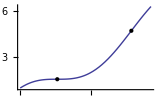

```mathematica
f[x_]:=x+Cos[x]
g[x_]=f''[x];
xs=x/.Solve[g[x]==0&&0≤x≤2π,x]
%//N
Show[{
Plot[f[x],{x,0,2Pi},PlotRange->{0,2Pi},ImageSize->160],
Graphics[{PointSize[Medium],Point[{xs[[1]],f[xs[[1]]]}]}],
Graphics[{PointSize[Medium],Point[{xs[[2]],f[xs[[2]]]}]}]
},PlotRange->All]
```

```mathematica
a=π/3;(* falls in (0,π/2) *)
b=π;(* falls in (π/2,(3π)/2) *)
c=(7π)/4;(* falls in ((3π)/2,2π) *)
```

```mathematica
g[a]*g[b]>0
```

False

Because f''(a) and f''(b) have different signs, x=π/2 is a point of inflection.

```mathematica
g[b]*g[c]>0
```

False

Since f''(b) and f''(c) have different signs, x=(3π)/2 is also a point of inflection.

## Finding equations of tangent lines using derivative

Now, we will use built-in command to find the slope of f(x) at a point x=x_0. The tangent line of f(x) at x=x_0 is given by

y=f(x_0)+f'(x_0)(x-x_0).

The following function allows you to explore the tangent lines of a function at different points.

```mathematica
ExploreTangentLine[func_,{x_,xmin_,xmax_},plotRange_] :=
Manipulate[
 Module[
{f, fPrime},
f[X_]=func/.x->X;
fPrime[X_]=f'[X];

Show[{
Plot[{f[x],fPrime[x],f[x0]+fPrime[x0](x-x0)},{x,xmin,xmax},PlotStyle->{{},{Dashed, Gray},{}},plotRange,ImageSize->320],
Graphics[{Red,PointSize[Medium],Point[{x0,f[x0]}]}]
}]],
{{x0,xmin+(xmax-xmin)/3,Style[Subscript[x, 0]]},xmin,xmax}
]
```

```mathematica
ExploreTangentLine[x Sin[x],{x,-2Pi,2Pi},PlotRange->{-7,7}]
```

Example 12
For f(x)=x^2, find the equation of the tangent line at x=-1.

```mathematica
f[x_]:=x^2
x0=-1;
g[x_]=f[x0]+f'[x0](x-x0);
%//Simplify//TraditionalForm
```

-2 x-1

Example 13
Refer to Example 12. Use the tangent line of f(x)=x^2 to approximate the value of f(x) at x=-0.99,-1.02, -1.5.

```mathematica
g[-0.99]
```

0.98

```mathematica
Abs[%-f[-0.99]] (* absolute error; best approximation *)
```

0.0001

```mathematica
g[-1.02]
```

1.04

```mathematica
Abs[%-f[-1.02]]
```

0.0004

```mathematica
g[-1.5]
```

2.

```mathematica
Abs[%-f[-1.5]] (* worst approximation *)
```

0.25

From the above calculation, we can see that, in general, if a point is closer to the point where the equation of a tangent line to f(x) is established, we obtain a better approximation, i.e., with a smaller error, at that point when using the tangent line to approximate f(x).

Example 14
Plot y=x^2-2x+2  for -2≤x≤3 together with its tangent lines at x=-1 and 2.

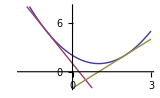

```mathematica
f[x_]:=x^2-2x+2
g[x_,x0_]:=f[x0]+f'[x0](x-x0)
Plot[{f[x],g[x,-1],g[x,2]},{x,-2,3},PlotRange->{-2,8},ImageSize->160]
```

## Three difference quotients

If f(x) is differentiable at x=x_0, then

f'(x_0)=limit_(h→0)(f(x_0+h)-f(x_0))/h=limit_(h→0)(f(x_0)-f(x_0-h))/h=limit_(h→0)(f(x_0+h)-f(x_0-h))/(2h).

Analytically, the three limits are exactly the same. But, with numerical computing, because no computer can take a value as large (∞) or as small (0) as we please, we cannot assign an infinitesimal to h. Instead, we have to let h assume some small quantity, a fixed number. In this sense, computer cannot take limit. That Mathematica can do it is simply because it is a system which attempts to do symbolic computing based on a library of mathematical rules, such as d/(d x)x^n=n x^(n-1),d/(d x)sin x=cos x,d/(d x)e^x=e^x, etc.

When we have to use a small fixed h to replace the infinitesimal h, we will lose preciseness. But when h is sufficiently small, we expect that f'(x_0)≈(f(x_0+h)-f(x_0))/h (forward difference quotient), f'(x_0)≈(f(x_0)-f(x_0-h))/h(backward difference quotient), and f'(x_0)≈(f(x_0+h)-f(x_0-h))/(2h)(central difference quotient). Using Taylor series expansion of f(x) at x=x_0, we can show that, analytically, the central difference quotient produces better approximation to the exact value f'(x_0).

Example 15
For sin x, letting h=0.01, compute the three difference quotients at x=π/3, and compare your results with the exact value of sin' π/3.

```mathematica
f[x_]:=Sin[x];
h=0.01;
x0=π/3;
exact=f'[x0] (* "exact" value of f'(x0) *)
```

1/2

```mathematica
(f[x0+h]-f[x0])/h (* forward difference quotient *)
```

0.495662

```mathematica
Abs[%-exact]
```

0.00433842

```mathematica
(f[x0]-f[x0-h])/h (* backward difference quotient *)
```

0.504322

```mathematica
Abs[%-exact]
```

0.00432176

```mathematica
(f[x0+h]-f[x0-h])/(2h) (* central difference quotient *)
```

0.499992

```mathematica
Abs[%-exact]
```

8.33329×10^-6

Indeed, the central difference quotient formula does give a much better approximation for f'(π/3) with h=0.01. A little more computation indicates that the absolute errors of the central difference quotient formula are 8.33334×10^-8,8.33833×10^-10, and 7.82668×10^-12 with h=0.001, h=0.0001, and h=0.00001, respectively.

The forward and backward difference quotients in this case show no big difference.

© 2015-2024 by David Wang, dwang@liberty.edu